```mathematica
η=1*10^-2;
dt=0.1;
T=295;
dx=8*10^-7/20;
v=dx^3;
kb=1.3806*10^-16;
R=(5*10^-8)/2;
```

```mathematica
χ=(kb T)/(6 π η R)
```

8.64269×10^-6

```mathematica
((2 χ)/dx^2)^-1
```

9.25638×10^-11

```mathematica
χ*1.01
```

7.92403×10^-6

```mathematica
((1.6*10^-19)^2)/((8*10^-7)^2)
```

4.×10^-26

```mathematica
1/(8*10^-7)
```

```mathematica
dx=(25*10^-7)/64;
F=1;
V=(25*10^-7)^3;
U=142076186.21676001;

araw=Solve[F==6 π η a U (1.0+1.7601 ((4/3 π a^3)/V)^(1/3)),a][[1,1,2]];
araw/dx
```

0.91851

```mathematica
χ=(kb T)/(6 π η R)
```

```mathematica
Solve[6 π η Rt == 6 π η Rw + 6 π η Rd,Rd]
```

{{Rd→Rt-Rw}}

```mathematica
Clear[srf]
eps =10^-12; σ=5*10^-8;q=4.8*10^-10;
srf[r_]=4 eps ((6 (σ/2)^6)/r^7-(12 (σ/2)^12)/r^13);
cf[r_]=-q^2/r^2;
```

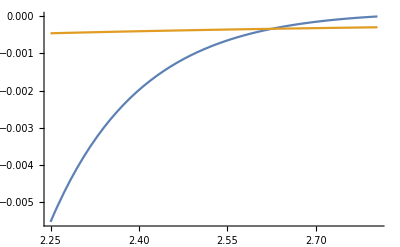

```mathematica
Plot[{srf[r],cf[r]},{r,0.9(σ/2),1.122(σ/2)},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
srf[σ/2.0]
cf[σ/2]
```

-0.00096

-0.00036864